```mathematica
<<SimulationTools`
```

## Exact plane wave solution

```mathematica
ClearAll[omega,nx,ny,nz,nt,w];
omega[wavenumber_]:=Sqrt[Sum[wavenumber⟦i⟧^2,{i,1,3}]];
nx[wavenumber_,spaceoffset_,x_]:=wavenumber⟦1⟧*(x-spaceoffset⟦1⟧);
ny[wavenumber_,spaceoffset_,y_]:=wavenumber⟦2⟧*(y-spaceoffset⟦2⟧);
nz[wavenumber_,spaceoffset_,z_]:=wavenumber⟦3⟧*(z-spaceoffset⟦3⟧);
nt[wavenumber_,timeoffset_,t_]:=omega[wavenumber]*(t-timeoffset);
w[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=2π(nx[wavenumber,spaceoffset,x]+ny[wavenumber,spaceoffset,y]+nz[wavenumber,spaceoffset,z]+nt[wavenumber,timeoffset,t]);

ClearAll[Phi,KPhi];
Phi[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=Cos[w[wavenumber,spaceoffset,timeoffset,t,x,y,z]]
KPhi[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=-1/2D[Phi[wavenumber,spaceoffset,timeoffset,tt,x,y,z],tt]//.tt->t;

ClearAll[PhiRHS,KPhiRHS];
PhiRHS[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=-2KPhi[wavenumber,spaceoffset,timeoffset,t,x,y,z];
KPhiRHS[wavenumber_,spaceoffset_,timeoffset_,t_,x_,y_,z_]:=-1/2Laplacian[Phi[wavenumber,spaceoffset,timeoffset,t,xx,yy,zz],{xx,yy,zz}]//.{xx->x,yy->y,zz->z};
```

```mathematica
Phi[{1,1,1},{0,0,0},0,0,x,y,z]
KPhiRHS[{1,1,1},{0,0,0},0,0,x,y,z]
```

Cos[2 π (x+y+z)]

6 π^2 Cos[2 π (x+y+z)]

## Invariants

```mathematica
ClearAll[function];
function="K_Phi_rhs";

ClearAll[dirs];
dirs={
NotebookDirectory[]<>"Test_Multipatch_coarse",
NotebookDirectory[]<>"Test_Multipatch_medium",
NotebookDirectory[]<>"Test_Multipatch_fine"
};
```

## Transform GF on a patch to cartesian coordiantes

```mathematica
ClearAll[Patch2Cartesian];
Patch2Cartesian[dir_,function_,map_]:=Module[
{xgf,local2global,gf,gf1d,minX,maxX,points,dX,temp},

(* Read the Grif GF and make it a interpolating function *)
xgf=ReadGridFunction[dir,"x","xyz",Iteration->0,Map->map];
local2global=Slab[xgf,0,0,All]//ToList//Interpolation;

(* Read the grid function in the specified map and create a 1d slab *)
gf=ReadGridFunction[dir,function,"xyz",Iteration->0,Map->map];
gf1d=Slab[gf,0,0,All];

minX=local2global[MinCoordinates[gf1d]⟦1⟧];
maxX=local2global[MaxCoordinates[gf1d]⟦1⟧];
points=Dimensions[gf1d]⟦1⟧-1;
dX=Abs[(maxX-minX)]/points;

gf1d=ToList[gf1d];

(* Applay the coordinate transformation to the grid function *)
Block[
{i},
For[i=1,i≤Length[gf1d],i++,
gf1d⟦i,1⟧=local2global[gf1d⟦i,1⟧];
]
];

Reverse[gf1d];

Return[{minX,maxX,points,dX,ToDataRegion[gf1d⟦All,2⟧,{Min[maxX,minX]},{dX}]}];
];
```

## Get GF on the central cartesian patch

```mathematica
ClearAll[CartesianData];
CartesianData[dir_,function_]:=Module[
{gf,gf1d,minX,maxX,points,dX},

(* Read the grid function in the specified map and create a 1d slab *)
gf=ReadGridFunction[dir,function,"xyz",Iteration->0,Map->0];
gf1d=Slab[gf,All,0,0];

minX=MinCoordinates[gf1d]⟦1⟧;
maxX=MaxCoordinates[gf1d]⟦1⟧;
points=Dimensions[gf1d]⟦1⟧-1;
dX=Abs[(maxX-minX)]/points;

Return[{minX,maxX,points,dX,gf1d}];
];
```

## Error plot

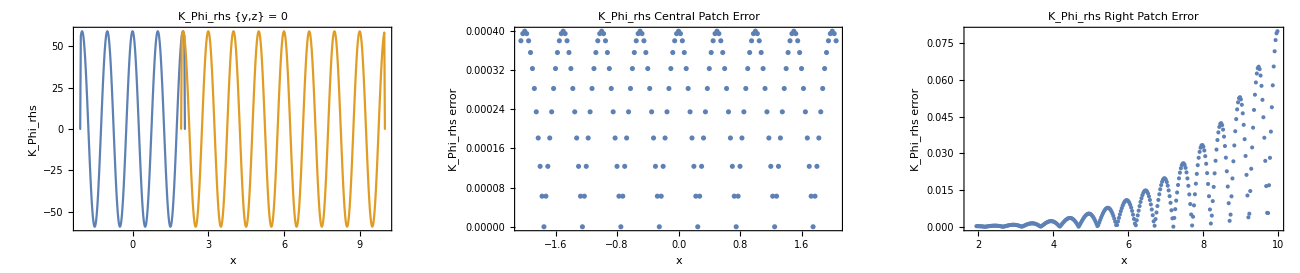

```mathematica
ClearAll[dirIndex];
dirIndex=3;

ClearAll[pc,p2];
pc=CartesianData[dirs⟦dirIndex⟧,function];
p2=Patch2Cartesian[dirs⟦dirIndex⟧,function,1];

ClearAll[ac,a2];
ac=ToDataRegion[Table[KPhiRHS[{1,1,1},{0,0,0},0,0,x,0,0],{x,Min[pc⟦1⟧,pc⟦2⟧],Max[pc⟦1⟧,pc⟦2⟧],pc⟦4⟧}],{Min[pc⟦1⟧,pc⟦2⟧]},{pc⟦4⟧}];
a2=ToDataRegion[Table[KPhiRHS[{1,1,1},{0,0,0},0,0,x,0,0],{x,Min[p2⟦1⟧,p2⟦2⟧],Max[p2⟦1⟧,p2⟦2⟧],p2⟦4⟧}],{Min[p2⟦1⟧,p2⟦2⟧]},{p2⟦4⟧}];

GraphicsRow[
{
ListPlot[
{
pc⟦5⟧,
p2⟦5⟧
},
Axes->False,
Frame->True,
PlotRange->Full,
Joined->True,
InterpolationOrder->1,

FrameLabel->{"x",function},
PlotLabel->function<>" {y,z} = 0"
]
,
ListPlot[
{
Abs[ac-pc⟦5⟧]⟦3;;-3⟧
},
Axes->False,
Frame->True,
PlotRange->{Full,Full},

FrameLabel->{"x",function<>" error"},
PlotLabel->function<>" Central Patch Error"
]
,
ListPlot[
{
Abs[a2-p2⟦5⟧]⟦3;;-3⟧
},
Axes->False,
Frame->True,
PlotRange->{Full,Full},

FrameLabel->{"x",function<>" error"},
PlotLabel->function<>" Right Patch Error"
]
},
ImageSize->1.3*10^3
]

Export[dirs⟦dirIndex⟧<>"_data_central.dat",pc⟦5⟧//ToList,"Table"];
Export[dirs⟦dirIndex⟧<>"_data_right.dat",p2⟦5⟧//ToList,"Table"];
Export[dirs⟦dirIndex⟧<>"_error_central.dat",Abs[ac-pc⟦5⟧]⟦3;;-3⟧//ToList,"Table"];
Export[dirs⟦dirIndex⟧<>"_error_right.dat",Abs[a2-p2⟦5⟧]⟦3;;-3⟧//ToList,"Table"];
```

## Convergence

```mathematica
ClearAll[pc1,p21];
pc1=CartesianData[dirs⟦1⟧,function];
p21=Patch2Cartesian[dirs⟦1⟧,function,1];

ClearAll[pc2,p22];
pc2=CartesianData[dirs⟦2⟧,function];
p22=Patch2Cartesian[dirs⟦2⟧,function,1];

ClearAll[pc3,p23];
pc3=CartesianData[dirs⟦3⟧,function];
p23=Patch2Cartesian[dirs⟦3⟧,function,1];
```

InterpolatingFunction::dmval: Input value {10.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

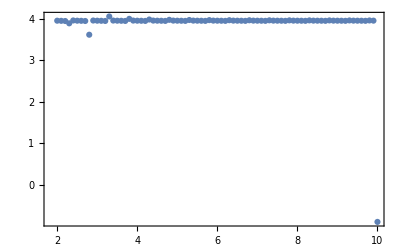

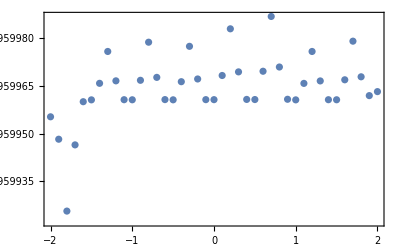

InterpolatingFunction::dmval: Input value {10.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
ListPlot[
Log[WithResampling[(p21⟦5⟧-p22⟦5⟧)/(p22⟦5⟧-p23⟦5⟧)]]/Log[2],
Axes->False,
Frame->True,
PlotRange->Full
]
ListPlot[
Log[WithResampling[(pc1⟦5⟧-pc2⟦5⟧)/(pc2⟦5⟧-pc3⟦5⟧)]]/Log[2],
Axes->False,
Frame->True,
PlotRange->Full
]

Export["Test_Multipatch_convergence_right.dat",ToList[Log[WithResampling[(p21⟦5⟧-p22⟦5⟧)/(p22⟦5⟧-p23⟦5⟧)]]/Log[2]],"Table"];
Export["Test_Multipatch_convergence_center.dat",ToList[Log[WithResampling[(pc1⟦5⟧-pc2⟦5⟧)/(pc2⟦5⟧-pc3⟦5⟧)]]/Log[2]],"Table"];
```